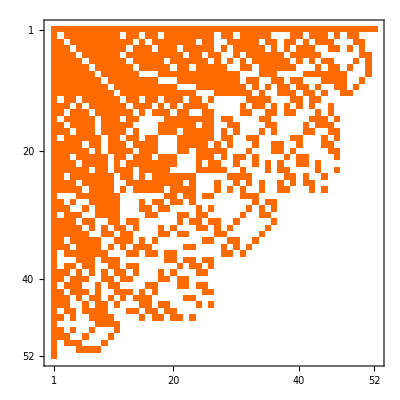

```mathematica
ConversionMatrix["F","C"]//MatrixPlot
```

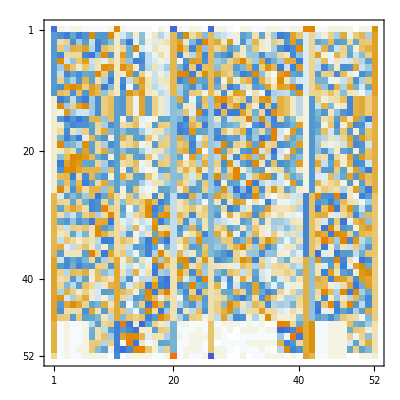
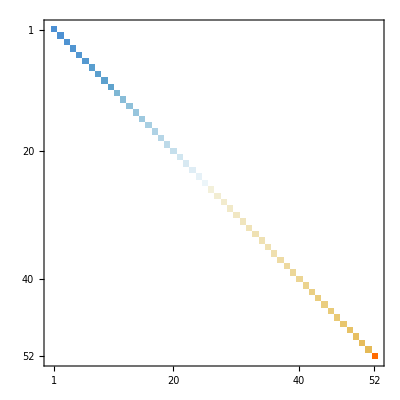

```mathematica
Map[MatrixPlot,JordanDecomposition[N[ConversionMatrix["F","C"]]]]
```

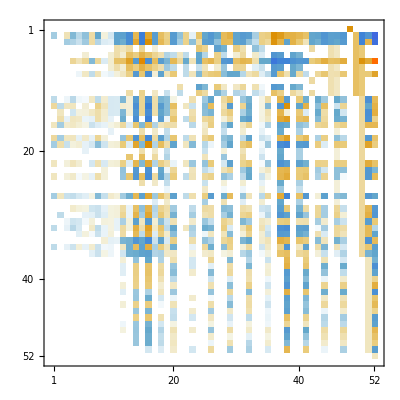
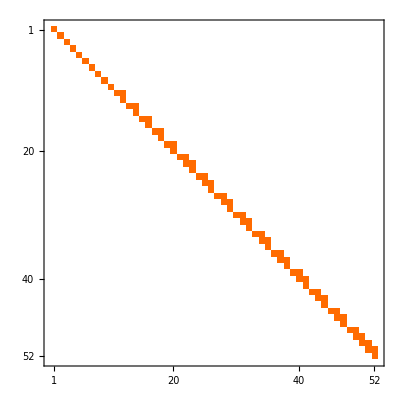

```mathematica
Map[MatrixPlot,JordanDecomposition[ConversionMatrix["E","C"]]]
```

```mathematica
allBases
```

{C,E,G,F,T}

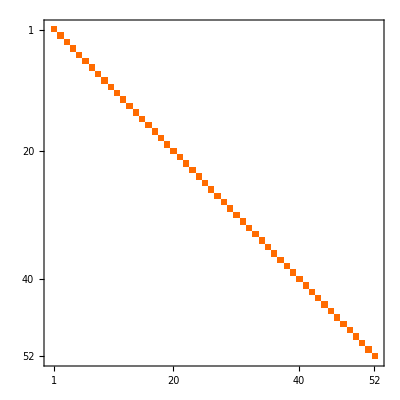
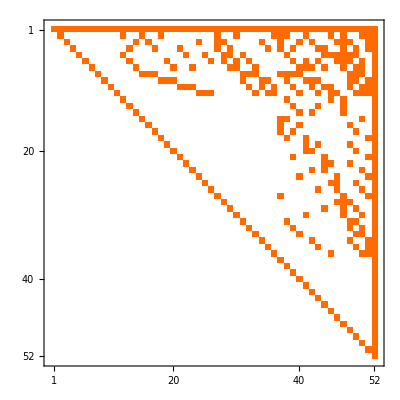
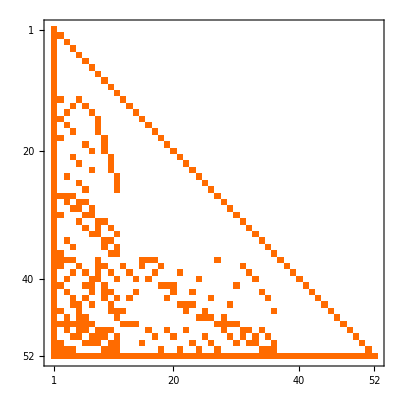
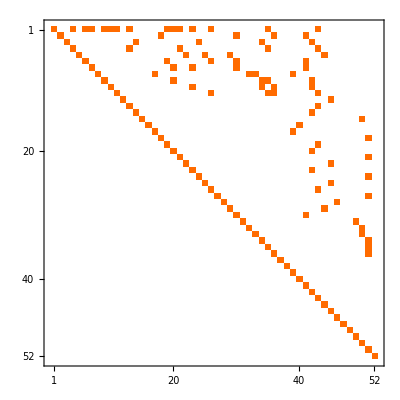
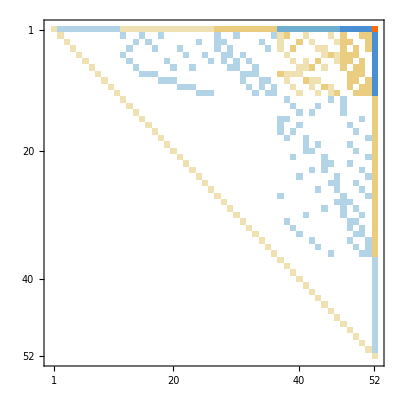
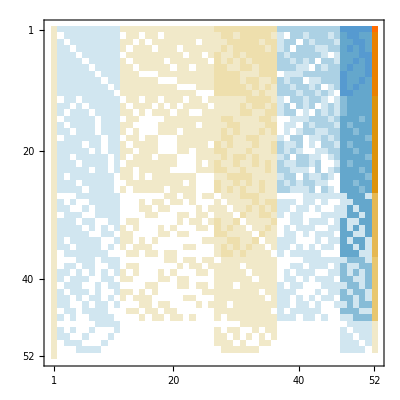
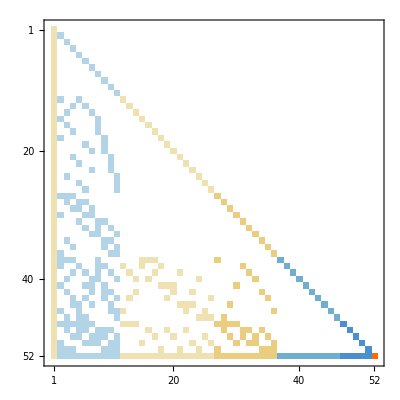
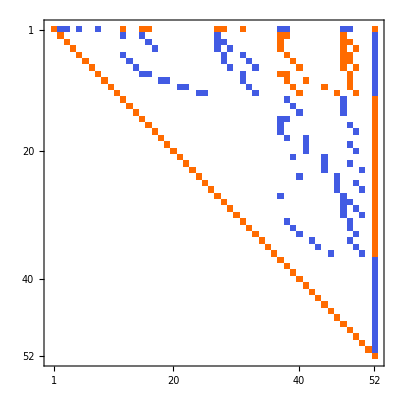
-Graphics-{C,C} | -Graphics-{E,C} | -Graphics-{G,C} | -Graphics-{F,C} | -Graphics-{T,C}
-Graphics-{C,E} | -Graphics-{E,E} | -Graphics-{G,E} | -Graphics-{F,E} | -Graphics-{T,E}
-Graphics-{C,G} | -Graphics-{E,G} | -Graphics-{G,G} | -Graphics-{F,G} | -Graphics-{T,G}
-Graphics-{C,F} | -Graphics-{E,F} | -Graphics-{G,F} | -Graphics-{F,F} | -Graphics-{T,F}
-Graphics-{C,T} | -Graphics-{E,T} | -Graphics-{G,T} | -Graphics-{F,T} | -Graphics-{T,T}

```mathematica
Monitor[TableForm[Table[Table[Labeled[MatrixPlot[ConversionMatrix[base1,base2]],{base1,base2}],{base1,allBases}],{base2,allBases}]],{base1,base2}]
```

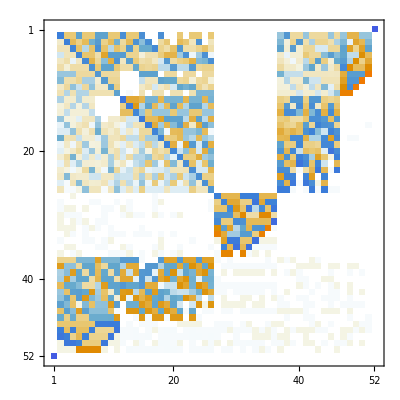
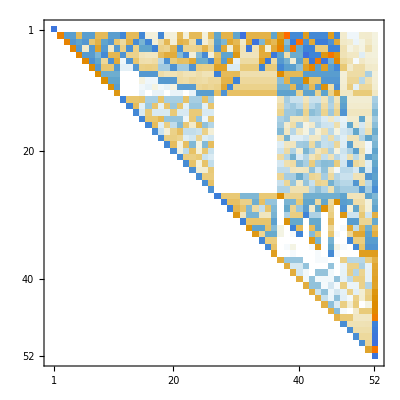
{-Graphics-{base1,base2},-Graphics-{base1,base2}}

```mathematica
Map[Labeled[MatrixPlot[#],{base1,base2}]&,QRDecomposition[N[ConversionMatrix["G","F"]]]]
```

```mathematica
VectorSize[vect_]:=Total[Map[If[#==0,0,1]&,vect]]
```

```mathematica
VectorSize[BaseCoeff[1,"C"]]
```

37

```mathematica
Table[base->Total[Table[VectorSize[BaseCoeff[k,base]],{k,Keys[allGraphs5]}]],{base,allBases}]
```

{C→15926,E→26778,G→18766,F→59016,T→20518}

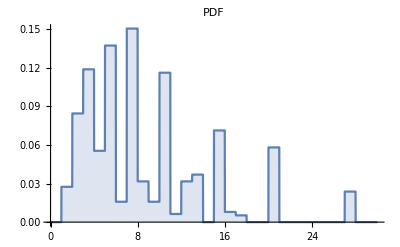
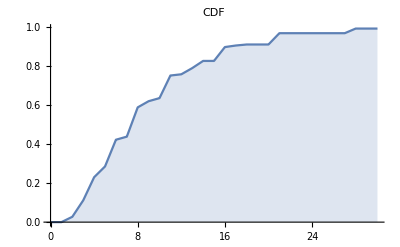
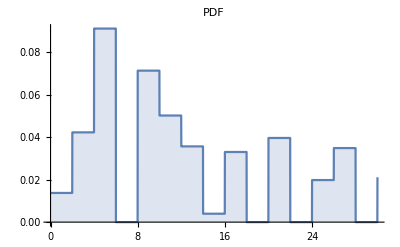
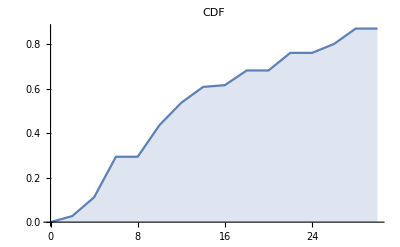
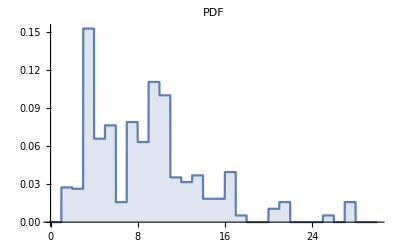
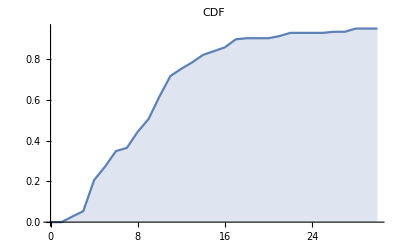
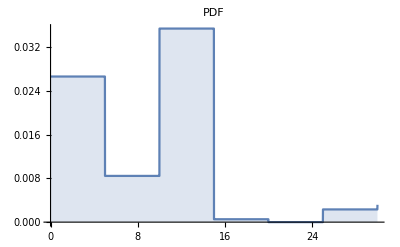
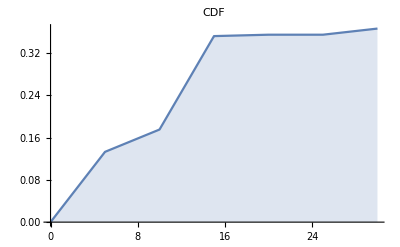
{C→{-Graphics-,-Graphics-},E→{-Graphics-,-Graphics-},G→{-Graphics-,-Graphics-},F→{-Graphics-,-Graphics-},T→{-Graphics-,-Graphics-}}

```mathematica
Table[base->With[{d=HistogramDistribution[Sort[Table[VectorSize[BaseCoeff[k,base]],{k,Keys[allGraphs5]}]]]},DiscretePlot[#[d,x],{x,0,30,.01},PlotLabel->#]&/@{PDF,CDF}],{base,allBases}]
```

```mathematica
Table[base->N[Mean[Table[VectorSize[BaseCoeff[k,base]],{k,Keys[allGraphs5]}]]],{base,allBases}]
```

{C→8.40422,E→14.1309,G→9.9029,F→31.143,T→10.8274}

```mathematica
Table[base->N[StandardDeviation[Table[VectorSize[BaseCoeff[k,base]],{k,Keys[allGraphs5]}]]],{base,allBases}]
```

{C→6.19092,E→10.9794,G→8.77383,F→17.5504,T→7.3589}

```mathematica
Table[base->N[Mean[Table[VectorSize[BaseCoeff[k,base]],{k,Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&]}]]],{base,allBases}]
```

{C→11.7041,E→20.9297,G→7.04492,F→32.1572,T→15.7979}

```mathematica
Table[base->Total[Table[VectorSize[BaseCoeff[k,base]],{k,Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&]}]],{base,allBases}]
```

{C→11985,E→21432,G→7214,F→32929,T→16177}

```mathematica
52*Length[Keys[allGraphs5]]
```

98540

```mathematica
Table[base->Total[Table[VectorSize[BaseCoeff[k,base]],{k,Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==4&]}]],{base,allBases}]
```

{C→3370,E→4700,G→6950,F→19390,T→3770}

```mathematica
Table[base->Total[Table[VectorSize[BaseCoeff[k,base]],{k,Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==3&]}]],{base,allBases}]
```

{C→525,E→600,G→3610,F→5705,T→525}

```mathematica
Table[base->Total[Table[VectorSize[BaseCoeff[k,base]],{k,Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==2&]}]],{base,allBases}]
```

{C→45,E→45,G→940,F→940,T→45}

```mathematica
Table[
e->Sort[Table[{Total[Table[VectorSize[BaseCoeff[k,base]],{k,Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&&EdgeCount[allGraphs5[#,"graph"]]==e&]}]],base},{base,allBases}]],
{e,0,10}
]//TableForm
```

0→{{1,E},{1,F},{1,G},{16,T},{52,C}}
1→{{10,F},{20,E},{142,T},{370,C},{370,G}}
2→{{135,F},{180,E},{465,G},{640,T},{1215,C}}
3→{{930,E},{1250,F},{1250,G},{1767,T},{2370,C}}
4→{{2100,G},{2880,E},{3025,C},{3235,T},{7285,F}}
5→{{1692,G},{2622,C},{4038,T},{5154,E},{9702,F}}
6→{{860,G},{1550,C},{3449,T},{5770,E},{7880,F}}
7→{{360,G},{610,C},{1983,T},{4130,E},{4670,F}}
8→{{105,G},{150,C},{734,T},{1545,F},{1845,E}}
9→{{10,G},{20,C},{158,T},{450,F},{470,E}}
10→{{1,C},{1,F},{1,G},{15,T},{52,E}}

```mathematica
Table[
e->Sort[Table[{N[Mean[Table[VectorSize[BaseCoeff[k,base]],{k,Select[Keys[allGraphs5],EdgeCount[allGraphs5[#,"graph"]]==e&]}]]],base},{base,allBases}]],
{e,0,10}
]//TableForm
```

0→{{1.,E},{4.36538,T},{6.88462,C},{6.88462,F},{46.1154,G}}
1→{{2.,E},{4.60625,T},{7.5625,C},{10.8438,F},{23.7813,G}}
2→{{4.,E},{6.35185,T},{8.94444,C},{11.7222,G},{20.6667,F}}
3→{{7.34783,E},{8.65797,T},{9.01449,G},{9.72464,C},{31.4203,F}}
4→{{8.5,G},{9.73611,C},{11.375,T},{12.3333,E},{37.6528,F}}
5→{{6.,G},{8.78846,C},{14.,T},{19.0192,E},{38.3077,F}}
6→{{4.,G},{7.09091,C},{15.9045,T},{26.9091,E},{37.8636,F}}
7→{{3.,G},{5.08333,C},{16.525,T},{34.4167,E},{38.9167,F}}
8→{{2.33333,G},{3.33333,C},{16.3111,T},{34.3333,F},{41.,E}}
9→{{1.,G},{2.,C},{15.8,T},{45.,F},{47.,E}}
10→{{1.,C},{1.,F},{1.,G},{15.,T},{52.,E}}

```mathematica
Table[base->N[Mean[Table[VectorSize[BaseCoeff[k,base]],{k,Keys[allGraphs5]}]]],{base,allBases}]
```

{C→8.40422,E→14.1309,G→9.9029,F→31.143,T→10.8274}

```mathematica
Table[base->N[Mean[Table[VectorSize[BaseCoeff[k,base]],{k,Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&]}]]],{base,allBases}]
```

{C→11.7041,E→20.9297,G→7.04492,F→32.1572,T→15.7979}

```mathematica
Flatten[Table[{a,x},{x,0,10},{a,0,10}],1]
```

{{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{0,1},{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{7,1},{8,1},{9,1},{10,1},{0,2},{1,2},{2,2},{3,2},{4,2},{5,2},{6,2},{7,2},{8,2},{9,2},{10,2},{0,3},{1,3},{2,3},{3,3},{4,3},{5,3},{6,3},{7,3},{8,3},{9,3},{10,3},{0,4},{1,4},{2,4},{3,4},{4,4},{5,4},{6,4},{7,4},{8,4},{9,4},{10,4},{0,5},{1,5},{2,5},{3,5},{4,5},{5,5},{6,5},{7,5},{8,5},{9,5},{10,5},{0,6},{1,6},{2,6},{3,6},{4,6},{5,6},{6,6},{7,6},{8,6},{9,6},{10,6},{0,7},{1,7},{2,7},{3,7},{4,7},{5,7},{6,7},{7,7},{8,7},{9,7},{10,7},{0,8},{1,8},{2,8},{3,8},{4,8},{5,8},{6,8},{7,8},{8,8},{9,8},{10,8},{0,9},{1,9},{2,9},{3,9},{4,9},{5,9},{6,9},{7,9},{8,9},{9,9},{10,9},{0,10},{1,10},{2,10},{3,10},{4,10},{5,10},{6,10},{7,10},{8,10},{9,10},{10,10}}

```mathematica
Select[Flatten[Table[{a,x},{x,0,10},{a,0,10}],1],CoprimeQ[#[[1]],#[[2]]]&]
```

{{1,0},{0,1},{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{7,1},{8,1},{9,1},{10,1},{1,2},{3,2},{5,2},{7,2},{9,2},{1,3},{2,3},{4,3},{5,3},{7,3},{8,3},{10,3},{1,4},{3,4},{5,4},{7,4},{9,4},{1,5},{2,5},{3,5},{4,5},{6,5},{7,5},{8,5},{9,5},{1,6},{5,6},{7,6},{1,7},{2,7},{3,7},{4,7},{5,7},{6,7},{8,7},{9,7},{10,7},{1,8},{3,8},{5,8},{7,8},{9,8},{1,9},{2,9},{4,9},{5,9},{7,9},{8,9},{10,9},{1,10},{3,10},{7,10},{9,10}}

```mathematica
With[
{max=500},
Length[Select[Flatten[Table[{a,x},{x,0,max},{a,0,max}],1],CoprimeQ[#[[1]],#[[2]]]&]]
]
```

152233

```mathematica
Monitor[
With[
{max=500},
TableForm[
Select[
Table[With[{a=k[[1]],x=k[[2]]},FactorInteger[3x^2+3x a^2+a^6]],{k,Select[Flatten[Table[{a,x},{x,0,max},{a,0,max}],1],CoprimeQ[#[[1]],#[[2]]]&]}]
,
Max[Map[Last,#]]>5&
],TableDepth->1]
],k
]
```

{{3,1},{5,6},{59,1},{12401,1}}
{{5,6},{547,1},{6427,1},{203869,1}}
{{3,1},{5,6},{11,1},{702641213,1}}
{{7,6},{13,1},{191,1},{7127,1}}
{{3,1},{5,6},{251,1},{313141271,1}}
{{5,6},{53,1},{447417479,1}}
{{5,6},{17581,1},{23991853,1}}
{{5,6},{17,1},{37,1},{2801,1},{18661,1}}
{{3,1},{5,6},{47,1},{157,1},{1196843,1}}
{{5,6},{30931,1}}
{{5,6},{547264873,1}}
{{5,6},{17,1},{37,1},{307,1},{107201,1}}
{{5,8},{17,1},{1723,1},{4517,1}}